```mathematica
(* Define the given values *)

n=116; (* number of samples *)
X=17; (* the observed value of x *)
```

1. What is the conditional distribution of X, the number of samples containing Giardia cysts, given θ?

Given θ, X is distributed according to binomial distribution with number of trials being n and θ being the success probability:

```mathematica
ConditionalDistribution[θ_]:=BinomialDistribution[n, θ]
```

2. Before the experiment, the NIWA scientists elicited that the expected value of θ is 0.2 with a standard deviation of 0.16. Determine the parameters α and β of a Beta prior distribution for θ with this prior mean and standard deviation. (Round α and β to the nearest integer).

```mathematica
Clear[α, β];
PriorDist := BetaDistribution[α, β];
(* Solve equation for the α & β and set the values for them into the scope, rounding them *)
RoundSolution[a_ -> p_]:= a -> Round[p] ;
Set @@@(RoundSolution/@ 
Solve[
Mean[PriorDist] == 1/5 && 
StandardDeviation[PriorDist] == 4/25
][[1]]);

StringForm["α = ``, β = ``", α, β]
```

α = 1, β = 4

3. Find the posterior distribution of θ and summarize it by its posterior mean and standard deviation.

```mathematica
α′=α+X;
β′=β+n-X;

PosteriorDist = BetaDistribution[α′, β′];

StringForm["α′ = ``, β′ = ``", α′, β′]
```

α′ = 18, β′ = 103

4. Plot the prior, posterior and normalized likelihood.

```mathematica
(* Function to normalize the likelihood to look like a PDF *)
NormLikelihood[f_]:=With[{fac=∫_0^1 f[θ]ⅆθ},f[#]/fac&]
```

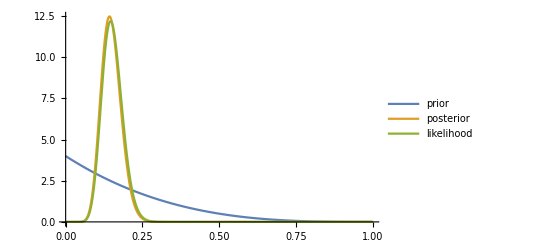

```mathematica
Plot[{
PDF[PriorDist][θ],
PDF[PosteriorDist][θ],
Evaluate[NormLikelihood[PDF[BinomialDistribution[n,#]][X]&][θ]],
}, 
{θ, 0, 1}, 
PlotLegends->LineLegend[{"prior", "posterior", "likelihood"} ], 
PlotRange->Full,
LabelStyle->{FontFamily->"Fira Code Light"}
]
```

5. Find the posterior probability that θ < 0.1

```mathematica
CDF[PosteriorDist, .1]
```

0.0530944

6. Find a central 95% posterior credible interval for θ

```mathematica
Lo := Quantile[PosteriorDist, .025]
Hi := Quantile[PosteriorDist, .975]
StringForm["The 95% credible interval is [``, ``]", NumberForm[Lo, {9, 3}], NumberForm[Hi, {9, 3}]]
```

The 95% credible interval is [0.091, 0.217]